```mathematica
PacletInstall["C:\\Users\\peter\\Documents\\GitHub\\MixedGraphPaclet\\Mixed Graphs\\build\\PeterBurbery__MixedGraphs-1.21.0.paclet"]
```

PacletObject[…]

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

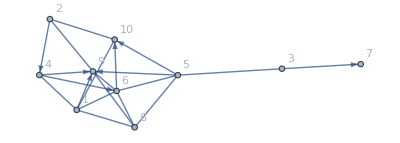

```mathematica
randomMixedGraph=RandomWeightedMixedGraph[{10,20},0.5,RandomReal[]&,VertexLabels->Automatic]
```

```mathematica
PeterBurbery`MixedGraphs`MixedGraphToDigraph[randomMixedGraph]
```

MixedGraphToDigraph[-Graphics-]

```mathematica
WeightedGraphQ[MixedGraphToDigraph[randomMixedGraph]]
```

True

```mathematica
VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]]
```

{3,5,6,7,9,10}

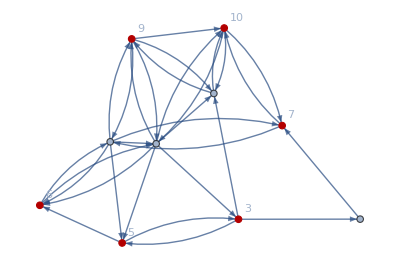

```mathematica
HighlightGraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]
```

```mathematica
VertexDegree[-Graphics-]
```

{8,10,5,2,5,5,5,6,7,7}

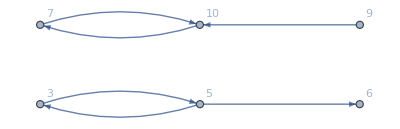

```mathematica
Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]
```

```mathematica
EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]
```

-Graphics-

## Convert to Undirected Graph

```mathematica
EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]
```

{1->2,1->5,1->6,1->7,1->9,2->3,2->5,2->6,2->8,2->9,2->10,3->4,3->5,3->5,3->8,4->7,5->3,5->6,5->6,6->1,6->2,7->1,7->10,7->10,8->9,8->10,9->1,9->2,9->8,9->10,9->10,10->2,10->7,10->8}

```mathematica
{First[#],Last[#]}&/@EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]
```

{{1,2},{1,5},{1,6},{1,7},{1,9},{2,3},{2,5},{2,6},{2,8},{2,9},{2,10},{3,4},{3,5},{3,5},{3,8},{4,7},{5,3},{5,6},{5,6},{6,1},{6,2},{7,1},{7,10},{7,10},{8,9},{8,10},{9,1},{9,2},{9,8},{9,10},{9,10},{10,2},{10,7},{10,8}}

```mathematica
Sort/@({First[#],Last[#]}&/@EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]])
```

{{1,2},{1,5},{1,6},{1,7},{1,9},{2,3},{2,5},{2,6},{2,8},{2,9},{2,10},{3,4},{3,5},{3,5},{3,8},{4,7},{3,5},{5,6},{5,6},{1,6},{2,6},{1,7},{7,10},{7,10},{8,9},{8,10},{1,9},{2,9},{8,9},{9,10},{9,10},{2,10},{7,10},{8,10}}

```mathematica
Union[Sort/@({First[#],Last[#]}&/@EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]),Sort/@({First[#],Last[#]}&/@EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]])]
```

{{1,2},{1,5},{1,6},{1,7},{1,9},{2,3},{2,5},{2,6},{2,8},{2,9},{2,10},{3,4},{3,5},{3,8},{4,7},{5,6},{7,10},{8,9},{8,10},{9,10}}

```mathematica
Complement[Union[Sort/@({First[#],Last[#]}&/@EdgeList[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]])],]
```

## Subgraphs

```mathematica
VertexDegree[EdgeAdd[-Graphics-,EdgeList@FindEdgeCover@Subgraph[-Graphics-,VertexList[-Graphics-,x_/;OddQ[VertexDegree[-Graphics-,x]]],VertexLabels->Automatic]]]
```

{8,10,6,2,7,6,6,6,8,9}

```mathematica
FindEdgeCover[-Graphics-]
```

{1->9,2->8,3->8,4->7,5->6,9->10}

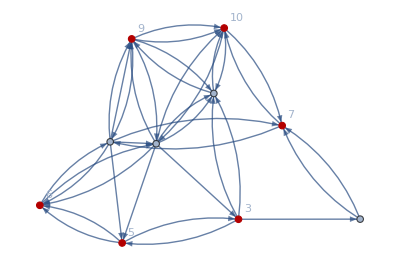

```mathematica
EdgeAdd[-Graphics-,FindEdgeCover[-Graphics-]]
```

```mathematica
VertexDegree[EdgeAdd[-Graphics-,FindEdgeCover[-Graphics-]]]
```

{9,11,6,3,6,6,6,8,9,8}

## Make graph even and solve minimum flow algorithm

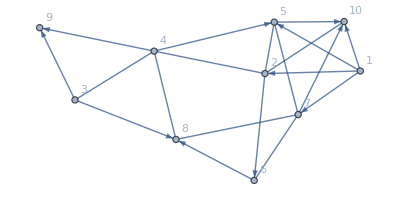

```mathematica
randomMixedGraph=RandomWeightedMixedGraph[{10,20},0.68,RandomInteger[{1,7}]&,VertexLabels->Automatic]
```

```mathematica
VertexDegree[randomMixedGraph]
```

{4,4,3,5,3,2,3,2,0,1}

```mathematica
EdgeList[randomMixedGraph,_->_]
```

{1->10,1->5,1->2,1->7,2->6,3->8,3->9,4->5,4->9,5->10,6->8,6->7,7->10}

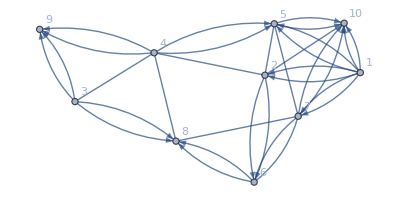

```mathematica
EdgeAdd[randomMixedGraph,EdgeList[randomMixedGraph,_->_]]
```

```mathematica
EdgeList[randomMixedGraph,_<->_]
```

{2<->4,2<->5,2<->10,3<->4,4<->8,5<->7,7<->8}

```mathematica
newEdges={}
```

{}

```mathematica
AppendTo[newEdges,{First[#]->Last[#],Last[#]->First[#]}]&/@EdgeList[randomMixedGraph,_<->_]
```

{{{2->4,4->2}},{{2->4,4->2},{2->5,5->2}},{{2->4,4->2},{2->5,5->2},{2->10,10->2}},{{2->4,4->2},{2->5,5->2},{2->10,10->2},{3->4,4->3}},{{2->4,4->2},{2->5,5->2},{2->10,10->2},{3->4,4->3},{4->8,8->4}},{{2->4,4->2},{2->5,5->2},{2->10,10->2},{3->4,4->3},{4->8,8->4},{5->7,7->5}},{{2->4,4->2},{2->5,5->2},{2->10,10->2},{3->4,4->3},{4->8,8->4},{5->7,7->5},{7->8,8->7}}}

```mathematica
newEdges
```

{{2->4,4->2},{2->5,5->2},{2->10,10->2},{3->4,4->3},{4->8,8->4},{5->7,7->5},{7->8,8->7}}

```mathematica
Flatten[%25]
```

{2->4,4->2,2->5,5->2,2->10,10->2,3->4,4->3,4->8,8->4,5->7,7->5,7->8,8->7}

```mathematica
Flatten[{First[#]->Last[#],Last[#]->First[#]}&/@EdgeList[randomMixedGraph,_<->_]]
```

{2->4,4->2,2->5,5->2,2->10,10->2,3->4,4->3,4->8,8->4,5->7,7->5,7->8,8->7}

```mathematica
Graph[%28]
```

-Graphics-

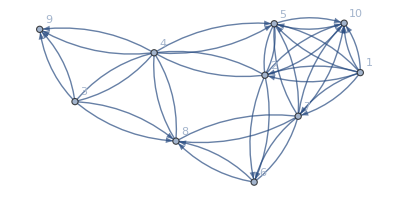

```mathematica
EdgeAdd[EdgeAdd[randomMixedGraph,EdgeList[randomMixedGraph,_->_]],Flatten[EdgeList[randomMixedGraph,_<->_]]]
```